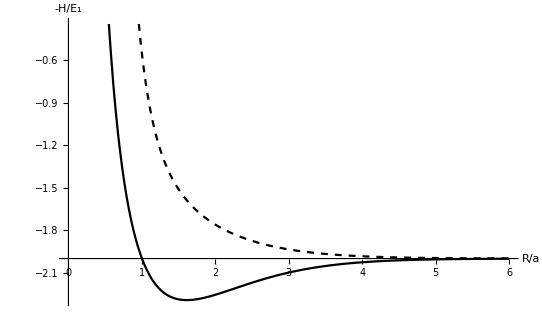

```mathematica
fD[x_]:=x^-1-(1+x^-1)Exp[-2x]
X[x_]:=(1+x)Exp[-x]
fI[x_]:=Exp[-x]*(1+x+x^2/3)
D2[x_]:=x^-1-Exp[-2x]*(x^2/6+3/4 x+11/8+x)
X2[x_]:=Exp[-2x]*(5/8-23/20 x-3/5 x^2-1/15x^3)+6/5x^-1*fI[x]^2*(EulerGamma+Log[x]+(fI[-x]/fI[x])^2ExpIntegralEi[-4x]-2(fI[x]/fI[x])ExpIntegralEi[-2x])
Hp[x_]:=-2*(1-1/x+(2fD[x]-D2[x]+(2fI[x]*X[x]-X2[x]))/(1+fI[x]^2))
Hm[x_]:=-2*(1-1/x+(2fD[x]-D2[x]-(2fI[x]*X[x]-X2[x]))/(1-fI[x]^2))
Plot[{Hp[x],Hm[x]},{x,0,6},AxesLabel->{"R/a","-H/E_1"},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]},AxesOrigin-> {0,-2.0},PlotStyle-> {Black,{Black,Dashed}}]
```